Import data:

```mathematica
data=Import["X:/CurrentProjects/Cyrus/B_Gradient.csv","Data"];
```

```mathematica
data//TableForm
```

| A02 | A03 | A04 | A05 | A06 | A07 | A08 | A09 | B01 | B02 | B03 | B04 | B05 | B06 | B07 | B08 | B09 | C01 | C02 | C03 | C04 | C05 | C06 | C07 | C08 | C09 | D01 | D02 | D03 | D04 | D05 | D06 | D07 | D08 | D09 | E01 | E02 | E03 | E04 | E05 | E06 | E07 | E08 | E09 | F01 | F02 | F03 | F04 | F05 | F06 | F07 | F08 | F09 | G01 | G02 | G03 | G04 | G05 | G06 | G07 | G08 | G09 | H01 | H02 | H03 | H04 | H05 | H06 | H07 | H08 | H09
B-1 R1_D0 | 0.378576 | 0.734198 | 0.464286 | 0 | 0 | 0.579194 | 0 | 0 | 0.0467033 | 0 | 0.0234765 | 0 | 0.0707701 | 0.762964 | 0 | 0 | 0 | 0.945373 | 0.0436836 | 0.547135 | 0.0338525 | 0 | 0 | 0 | 0 | 0.454591 | 0.0229543 | 0.128644 | 0 | 0 | 0.340183 | 0.0841431 | 0 | 0 | 0 | 0.357574 | 0 | 0.726864 | 0.714081 | 0.860458 | 0.733993 | 0.69224 | 0.537508 | 0.756085 | 0.82799 | 0.491577 | 0 | 0.804355 | 0.18838 | 0 | 0.662746 | 0.711311 | 0.399078 | 0.842748 | 0.894946 | 0 | 0.914744 | 0.823086 | 0.788938 | 0.735492 | 0.980315 | 0.243529 | 0.115907 | 1 | 0 | 0.458065 | 0.101035 | 0.00740169 | 0.0791935 | 0.13239 | 0.0416175
B-1 R2_D0 | 0.536916 | 0.82888 | 0.811616 | 0.158233 | 0.0542906 | 0.582838 | 0 | 0 | 0.0648785 | 0 | 0.18193 | 0.0115761 | 0.0665524 | 0.834587 | 0 | 0 | 0 | 0.920258 | 0.194434 | 0.67347 | 0 | 0 | 0.0463043 | 0 | 0 | 0.572532 | 0 | 0.392034 | 0.0805082 | 0.000443683 | 0.674599 | 0.162146 | 0.145165 | 0 | 0 | 0.398104 | 0 | 0.780821 | 0.727478 | 0.841767 | 0.86147 | 0.731471 | 0.444832 | 0.787738 | 0.752788 | 0.510437 | 0 | 0.894081 | 0.296037 | 0.0143592 | 0.774145 | 0.834224 | 0.510416 | 0.814763 | 0.878108 | 0 | 1 | 0.833075 | 0.842755 | 0.746597 | 0.964626 | 0.225149 | 0.333609 | 0.877705 | 0 | 0.403832 | 0.0181103 | 0.0590905 | 0.0601997 | 0.267662 | 0.0740748
B-1 R3_D0 | 0.483794 | 0.355786 | 0.424046 | 0 | 0 | 0.205183 | 0 | 0 | 0.0570453 | 0 | 0 | 0.0703227 | 0 | 0.752922 | 0 | 0 | 0 | 0.957773 | 0 | 0.464021 | 0.22581 | 0 | 0 | 0 | 0 | 0.39697 | 0 | 0.01176 | 0 | 0 | 0.219835 | 0.0242312 | 0 | 0 | 0 | 0.432179 | 0 | 0.761932 | 0.732437 | 0.814306 | 0.746189 | 0.710767 | 0.579629 | 0.705361 | 0.681272 | 0.50997 | 0 | 0.850819 | 0.0486521 | 0 | 0.754511 | 0.841027 | 0.382626 | 0.806624 | 0.901819 | 0 | 0.994571 | 0.886123 | 0.751832 | 0.756242 | 1 | 0.449819 | 0.246461 | 0.826612 | 0 | 0.422126 | 0.0323162 | 0.0183749 | 0.0429381 | 0.145008 | 0.0307276
B-3 R1_D0 | 0.593039 | 0.112191 | 0.00639116 | 0.0733687 | 0 | 0.0320853 | 0.140087 | 0.138964 | 0.0883102 | 0 | 0 | 0 | 0.357646 | 0.104331 | 0 | 0 | 0 | 0.410027 | 0.0414993 | 0.0238373 | 0 | 0 | 0 | 0 | 0 | 0.519281 | 0.186121 | 0.519627 | 0.136892 | 0 | 0.182407 | 0.171136 | 0 | 0 | 0 | 0.333808 | 0 | 0.0148119 | 0.157577 | 0.522909 | 0.781448 | 0.453297 | 0.202703 | 0.339206 | 0.598739 | 0.232586 | 0 | 0.582718 | 0.153906 | 0.134257 | 0.743447 | 0.57352 | 0.633372 | 0.282636 | 0.164097 | 0 | 0.47368 | 0.547048 | 0.444229 | 0.021419 | 1 | 0.333852 | 0.523686 | 0.60146 | 0 | 0.507406 | 0.125103 | 0.128514 | 0.0332945 | 0.459429 | 0.191864
B-3 R2_D0 | 0.448771 | 0.317798 | 0.125197 | 0 | 0 | 0.0758854 | 0 | 0 | 0.0455222 | 0 | 0 | 0 | 0 | 0.332371 | 0 | 0 | 0 | 0.439792 | 0 | 0.0254455 | 0 | 0 | 0 | 0 | 0 | 0.334582 | 0 | 0.459102 | 0 | 0 | 0.0000902 | 0.0316716 | 0 | 0 | 0 | 0.646831 | 0 | 0 | 0 | 0.162148 | 0.152538 | 0.240289 | 0 | 0.183397 | 1 | 0.111166 | 0 | 0.359531 | 0.0443492 | 0 | 0.412587 | 0.345906 | 0.420483 | 0.327724 | 0.180826 | 0 | 0.446018 | 0.412181 | 0.203293 | 0.0198962 | 0.915407 | 0.0677645 | 0.15723 | 0.342973 | 0 | 0.150823 | 0.0514324 | 0.0775547 | 0.0526506 | 0.264291 | 0.0543199
B-3 R3_D0 | 0.29302 | 0.0140335 | 0.069943 | 0 | 0 | 0.142328 | 0 | 0.112717 | 0.0598389 | 0 | 0 | 0 | 0.301945 | 0.309271 | 0 | 0 | 0 | 0.412726 | 0.0180471 | 0.352662 | 0 | 0 | 0 | 0 | 0 | 0.341323 | 0.0101603 | 0.129585 | 0 | 0 | 0.139858 | 0.314716 | 0 | 0 | 0 | 0.190743 | 0 | 0 | 0.113391 | 0.26818 | 0.491818 | 0.361644 | 0.0504926 | 0.278256 | 0.655056 | 0.0857167 | 0 | 0.367903 | 0.149794 | 0.0592776 | 0.502175 | 0.334306 | 0.711948 | 0.347526 | 0.265065 | 0 | 0.426871 | 0.48991 | 0.161722 | 0 | 1 | 0.122934 | 0.289399 | 0.299531 | 0 | 0.262763 | 0.0969435 | 0.207949 | 0.146538 | 0.329338 | 0.11384
B-6 R1_D0  | 0.642125 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.713852 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.62277 | 0.103985 | 0 | 0 | 0 | 0.0531309 | 0 | 0.73852 | 0.637192 | 1 | 0.66186 | 0 | 0.568501 | 0.266034 | 0.20038 | 0 | 0.795066 | 0.249715
B-6 R2_D0 | 0.533566 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0140315 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0298056 | 0 | 0 | 0 | 0 | 0 | 0.0278797 | 0 | 0 | 0.210565 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.178742 | 0.141049 | 0.0926266 | 0 | 0 | 0.0194424 | 0.0900587 | 0 | 0.186262 | 0.21836 | 0.315664 | 0.0974872 | 0 | 0.156456 | 0 | 0.0272377 | 0 | 0 | 1
B-6 R3_D0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
B-1_R3_NI_D28 | 0.368857 | 0.518661 | 0.0936455 | 0 | 0 | 0.132507 | 0 | 0 | 0.0613497 | 0 | 0 | 0 | 0.0204567 | 0.451833 | 0 | 0 | 0 | 0.870632 | 0 | 0.588157 | 0 | 0 | 0 | 0 | 0 | 0.207358 | 0 | 0.166875 | 0 | 0 | 0.492952 | 0.0472741 | 0 | 0 | 0 | 0.372366 | 0 | 0.665593 | 0.778054 | 0.77159 | 0.764101 | 0.600365 | 0.622012 | 0.660915 | 0.659519 | 0.551491 | 0 | 0.857152 | 0.042637 | 0 | 0.617067 | 0.760654 | 0.366498 | 0.831729 | 0.841517 | 0 | 0.955701 | 0.789729 | 0.767836 | 0.720972 | 1 | 0.420379 | 0.470813 | 0.983031 | 0 | 0.3856 | 0 | 0 | 0 | 0.0896239 | 0.0527115
B-1_R2_NI_D28 | 0.219225 | 0.155883 | 0.344 | 0 | 0.0634476 | 0.259839 | 0 | 0 | 0.00955773 | 0 | 0.0594674 | 0 | 0.160648 | 0.113043 | 0 | 0 | 0 | 0.99183 | 0 | 0.114431 | 0.157977 | 0 | 0 | 0 | 0 | 0.199246 | 0 | 0 | 0.00426825 | 0 | 0.25002 | 0.0805468 | 0 | 0 | 0.0237765 | 0.346513 | 0 | 0.586294 | 0.521616 | 0.821519 | 0.651418 | 0.33706 | 0.331352 | 0.509806 | 0.868863 | 0.238446 | 0 | 0.837231 | 0.219199 | 0 | 0.762602 | 0.89984 | 0.457933 | 0.769436 | 0.875488 | 0 | 0.894629 | 0.825342 | 0.761319 | 0.618922 | 0.959648 | 0.157768 | 0.191338 | 1 | 0 | 0.328917 | 0.120165 | 0 | 0.0111289 | 0.133625 | 0.0501977
B-1_R1_NI_D28 | 0.392464 | 0.217966 | 0.172984 | 0 | 0 | 0.185031 | 0 | 0.080212 | 0 | 0 | 0 | 0 | 0.0426446 | 0.473656 | 0 | 0 | 0 | 0.835412 | 0 | 0.127756 | 0 | 0 | 0 | 0 | 0 | 0.35051 | 0 | 0.0830624 | 0 | 0 | 0.169799 | 0.095377 | 0 | 0 | 0 | 0.242685 | 0 | 0.526544 | 0.652185 | 0.782323 | 0.743553 | 0.685209 | 0.638979 | 0.605598 | 0.578096 | 0.552933 | 0 | 0.801853 | 0.239745 | 0 | 0.655347 | 0.718501 | 0.3987 | 0.839242 | 0.893088 | 0 | 0.946889 | 0.781455 | 0.798423 | 0.71545 | 1 | 0.299336 | 0.491783 | 0.873335 | 0 | 0.497283 | 0 | 0.011023 | 0.0698125 | 0.237941 | 0.0412862
B-3_R3_NI_D28 | 0.364642 | 0.37946 | 0.202562 | 0.188202 | 0.102612 | 0.208498 | 0.12533 | 0.153133 | 0.0605809 | 0 | 0.254785 | 0 | 0.0176331 | 0.648343 | 0.0925954 | 0 | 0 | 0.606006 | 0.178077 | 0.441961 | 0.0192916 | 0 | 0.017022 | 0 | 0 | 0.366934 | 0.0105624 | 0.26406 | 0 | 0 | 0.0645527 | 0.111058 | 0 | 0.0521354 | 0 | 0.21092 | 0 | 0.716933 | 0.552976 | 0.825808 | 0.687144 | 0.576981 | 0.496759 | 0.437182 | 0.631168 | 0.219606 | 0 | 0.372084 | 0.16878 | 0 | 0.532113 | 0.561596 | 0.349824 | 0.757676 | 0.351876 | 0 | 0.920629 | 0.782009 | 0.813369 | 0.71571 | 1 | 0.216965 | 0.254523 | 0.789996 | 0 | 0.170831 | 0.0569147 | 0.0270606 | 0.0896057 | 0.264932 | 0.0177858
B-3_R2_NI_D28 | 0.392008 | 0.0794064 | 0.245616 | 0 | 0 | 0.0421454 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.6847 | 0 | 0 | 0 | 0.421919 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.462623 | 0 | 0.0159557 | 0 | 0 | 0 | 0.076941 | 0 | 0 | 0 | 0.356236 | 0 | 0.0954552 | 0.398474 | 0.515932 | 0.303066 | 0.0369819 | 0 | 0.64609 | 0.781923 | 0.0937805 | 0 | 0.446248 | 0 | 0 | 0.74522 | 0.274876 | 0.397776 | 0.158859 | 0 | 0 | 1 | 0.632553 | 0.262455 | 0 | 0.859143 | 0 | 0.129181 | 0.889706 | 0 | 0.155464 | 0 | 0 | 0 | 0.155975 | 0
B-3_R1_NI_D28 | 0.460149 | 0.514541 | 0.165492 | 0.455881 | 0 | 0.699355 | 0.0381472 | 0.0550868 | 0.0633912 | 0.330157 | 0.0725227 | 0.425806 | 0.508023 | 0.65469 | 0.000860215 | 0 | 0 | 0.482647 | 0.237386 | 0.685161 | 0.462233 | 0 | 0 | 0 | 0 | 0.427692 | 0.247411 | 0.467097 | 0.0228288 | 0 | 0.577634 | 0.327907 | 0.0231596 | 0 | 0 | 0.704615 | 0.0113813 | 0.526981 | 0.440364 | 0.522084 | 0.720165 | 0.455153 | 0.133532 | 0.549975 | 0.82938 | 0.376443 | 0 | 0.770256 | 0.231365 | 0.0735153 | 0.816609 | 0.649363 | 0.646121 | 0.563937 | 0.406981 | 0 | 0.760099 | 0.569859 | 0.633383 | 0.0963772 | 1 | 0.456807 | 0.48493 | 0.435335 | 0 | 0.482878 | 0.0741108 | 0.120033 | 0.0484367 | 0.434111 | 0.220778
B-6_R3_NI_D28 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.284714 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.88098 | 0.180863 | 0 | 0 | 0 | 0 | 0 | 0 | 0
B-6_R2_NI_D28 | 0.706566 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.153215 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.547196 | 0 | 0 | 0.109439 | 0 | 0 | 0.187551 | 0 | 0.949932 | 0.211081 | 0.368126 | 0 | 0 | 0.302052 | 0.256498 | 0 | 0.957182 | 0.223119 | 0.417373 | 0.134063 | 0 | 0.137483 | 0 | 0.00752394 | 0 | 0.111902 | 1
B-6_R1_NI_D28 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
B-1 R1_D28 | 0.574347 | 0.615359 | 0.507185 | 0.338599 | 0.418542 | 0.778141 | 0.458407 | 0.479047 | 0.373474 | 0.421317 | 0.377383 | 0.408176 | 0.624338 | 0.568796 | 0.239163 | 0.0374368 | 0.255413 | 0.934746 | 0.472483 | 0.85068 | 0.48393 | 0 | 0.0663216 | 0.0252025 | 0.125078 | 0.57444 | 0.317145 | 0.539778 | 0.283111 | 0.143757 | 0.857284 | 0.214027 | 0 | 0.05853 | 0.393313 | 0.462503 | 0.0814911 | 0.847438 | 0.873547 | 0.863901 | 0.853415 | 0.855523 | 0.764012 | 0.782744 | 0.58574 | 0.674823 | 0.136872 | 0.948354 | 0.5213 | 0.113058 | 0.836884 | 0.942244 | 0.757848 | 0.93584 | 0.851374 | 0 | 1 | 0.821421 | 0.869878 | 0.897616 | 0.959962 | 0.423639 | 0.434979 | 0.951503 | 0.0435873 | 0.86162 | 0.151402 | 0.0359292 | 0.428268 | 0.451443 | 0.194615
B-1 R2_D28 | 0.673555 | 0.900633 | 0.660699 | 0.450301 | 0.452189 | 0.773382 | 0.439271 | 0.498834 | 0.554794 | 0.403752 | 0.474742 | 0.377676 | 0.443381 | 0.833563 | 0.0383279 | 0.0700376 | 0.339396 | 0.896951 | 0.491739 | 0.737387 | 0.547382 | 0 | 0.413655 | 0.0342173 | 0.089876 | 0.678633 | 0.222286 | 0.542319 | 0.511832 | 0.178673 | 0.745052 | 0.494517 | 0.237252 | 0.229047 | 0.295371 | 0.734197 | 0.279135 | 0.798045 | 0.844673 | 0.795505 | 0.815725 | 0.751337 | 0.708978 | 0.689933 | 0.623054 | 0.66727 | 0.0837976 | 0.848784 | 0.568284 | 0.109588 | 0.720278 | 0.830326 | 0.631275 | 0.867622 | 0.864988 | 0 | 1 | 0.873748 | 0.778635 | 0.773017 | 0.900173 | 0.38677 | 0.480677 | 0.931692 | 0.18045 | 0.708073 | 0.42605 | 0.00750686 | 0.478487 | 0.326128 | 0.192131
B-1 R3_D28 | 0.543854 | 0.931894 | 0.78066 | 0.670967 | 0.627994 | 0.847801 | 0.443167 | 0.662818 | 0.690428 | 0.437854 | 0.608797 | 0.478848 | 0.615466 | 0.884168 | 0.366335 | 0.172144 | 0.299226 | 0.945262 | 0.435906 | 0.608564 | 0.400754 | 0 | 0.323159 | 0.17378 | 0.140685 | 0.647875 | 0.611088 | 0.547422 | 0.452344 | 0.0550959 | 0.654918 | 0.68136 | 0.49644 | 0.24614 | 0.342261 | 0.676483 | 0.12515 | 0.800667 | 0.814503 | 0.823759 | 0.859845 | 0.825114 | 0.75975 | 0.762399 | 0.553063 | 0.667165 | 0.10156 | 0.794606 | 0.599573 | 0.126708 | 0.797286 | 0.878823 | 0.672666 | 0.921142 | 0.840228 | 0 | 1 | 0.87834 | 0.767182 | 0.773524 | 0.880304 | 0.229156 | 0.355662 | 0.997554 | 0.404836 | 0.634756 | 0.410524 | 0.017311 | 0.590925 | 0.431777 | 0.38737
B-3 R1_D28  | 0.901605 | 0.771136 | 0.667098 | 0.737327 | 0.521108 | 0.868258 | 0.454414 | 0.610766 | 0.733134 | 0.394788 | 0.684947 | 0.660468 | 0.800443 | 0.710303 | 0.422537 | 0.0199996 | 0.308797 | 0.909442 | 0.537837 | 0.660776 | 0.424074 | 0 | 0.057979 | 0.129789 | 0.0649162 | 0.738864 | 0.479682 | 0.730302 | 0.36098 | 0.0524467 | 0.653092 | 0.134377 | 0 | 0.39279 | 0.31951 | 0.849356 | 0.32434 | 0.439683 | 0.670282 | 0.667801 | 0.775482 | 0.724704 | 0.575531 | 0.657197 | 0.770784 | 0.575816 | 0 | 0.739215 | 0.572106 | 0.0419969 | 0.911923 | 0.793572 | 0.844526 | 0.7795 | 0.201993 | 0 | 0.958289 | 0.764264 | 0.56159 | 0.595947 | 1 | 0.254001 | 0.389739 | 0.819938 | 0.131347 | 0.66161 | 0.163641 | 0.022634 | 0.6842 | 0.618977 | 0.0176286
B-3 R2_D28 | 0.802626 | 0.590544 | 0.758943 | 0.520579 | 0.469594 | 0.608345 | 0.423618 | 0.400997 | 0.633617 | 0.449857 | 0.590186 | 0.453434 | 0.67892 | 0.773756 | 0.0753304 | 0.111964 | 0.306813 | 0.791116 | 0.522283 | 0.478958 | 0.459031 | 0 | 0.199015 | 0.0778554 | 0 | 0.844984 | 0.228116 | 0.544083 | 0.254882 | 0 | 0.677342 | 0.746528 | 0.492677 | 0.227106 | 0.205244 | 0.8861 | 0.255092 | 0.773293 | 0.752735 | 0.75484 | 0.752904 | 0.751641 | 0.614995 | 0.688052 | 1 | 0.635784 | 0.181887 | 0.772641 | 0.630187 | 0.246023 | 0.83562 | 0.75101 | 0.800522 | 0.478495 | 0.565988 | 0 | 0.99091 | 0.753703 | 0.758101 | 0.761699 | 0.95819 | 0.348098 | 0.381218 | 0.950025 | 0.361628 | 0.731946 | 0.423049 | 0.196427 | 0.531816 | 0.767318 | 0.275356
B-3 R3_D28 | 0.643815 | 0.534716 | 0.591899 | 0.453333 | 0.494803 | 0.620997 | 0.355346 | 0.434051 | 0.54273 | 0.454786 | 0.416885 | 0.405722 | 0.493823 | 0.449711 | 0 | 0 | 0.109239 | 0.626422 | 0.448364 | 0.399248 | 0.571234 | 0 | 0.122537 | 0.0885389 | 0.141942 | 0.743447 | 0.245722 | 0.56007 | 0.30231 | 0.0236395 | 0.59748 | 0.362187 | 0.147454 | 0.208819 | 0.115521 | 0.647367 | 0.273018 | 0.411916 | 0.537078 | 0.650674 | 0.6621 | 0.608031 | 0.642117 | 0.64077 | 0.702012 | 0.432108 | 0 | 0.657393 | 0.350989 | 0.17664 | 0.704427 | 0.600472 | 0.681417 | 0.538653 | 0.355416 | 0 | 0.728591 | 0.742187 | 0.578565 | 0.515398 | 1 | 0.386842 | 0.535801 | 0.793753 | 0.399493 | 0.625477 | 0.487227 | 0.136535 | 0.544654 | 0.821907 | 0.175346
B-6 R1_D28  | 0.640898 | 0.691606 | 0.827117 | 0.544266 | 0.562312 | 0.913803 | 0.71956 | 0.143648 | 0.726379 | 0.39135 | 0.434373 | 0.433281 | 0.484177 | 0.701854 | 0 | 0.760059 | 0.773923 | 0.586046 | 0.472046 | 0.471481 | 0.591056 | 0 | 0.280478 | 0.315439 | 0.0463382 | 0.924842 | 0.261076 | 0.411618 | 0.0554174 | 0.0777954 | 0.710518 | 0.485759 | 0.381103 | 0.0774563 | 0 | 0.0987794 | 0.32497 | 0 | 0 | 0.697257 | 0.825347 | 0.499397 | 0.535262 | 0.0618219 | 0.280176 | 0.815853 | 0.657512 | 0.901899 | 0.802517 | 0 | 0.578624 | 0.415876 | 0.457241 | 0.348629 | 0.280967 | 0 | 0.865167 | 0.486099 | 0.512997 | 0.426349 | 0.958258 | 0.00904159 | 0.0803948 | 0.0629521 | 0.0415913 | 0.644552 | 0.039896 | 0.123945 | 0.185767 | 1 | 0.313366
B-6 R2_D28 | 0.628396 | 0.774995 | 0.707884 | 0.279776 | 0.324229 | 0.714342 | 0.109724 | 0.440989 | 0.851633 | 0.609237 | 0.682482 | 0 | 0 | 0.996428 | 0 | 0.628973 | 0.805304 | 0.781779 | 0.437092 | 0.528414 | 0.317951 | 0 | 0 | 0.102039 | 0 | 0.549017 | 0.116363 | 0.463467 | 0 | 0.0255097 | 1 | 0.349522 | 0.382176 | 0.439798 | 0 | 0.430056 | 0.0552769 | 0 | 0.089843 | 0.283421 | 0.449432 | 0.285874 | 0.347141 | 0 | 0.331301 | 0.987299 | 0.458669 | 0.930904 | 0.694894 | 0 | 0.229082 | 0.287281 | 0.114848 | 0.777413 | 0.102183 | 0 | 0.863179 | 0.201912 | 0.124698 | 0.152733 | 0.784232 | 0.0576583 | 0.178135 | 0.322064 | 0.178531 | 0.366228 | 0.200289 | 0 | 0.134548 | 0.597438 | 0.073462
B-6 R3_D28 | 0.776191 | 0.803599 | 0.85494 | 0.644852 | 0.692129 | 0.905829 | 0.464742 | 0.973218 | 0.895581 | 0.554293 | 0.56725 | 0 | 0.846915 | 1 | 0 | 0.825657 | 0.890649 | 0.944004 | 0.475198 | 0.691712 | 0.659441 | 0 | 0.335765 | 0.330763 | 0.726171 | 0.763339 | 0.0634292 | 0.882138 | 0 | 0 | 0 | 0.425872 | 0.329165 | 0.0104905 | 0 | 0 | 0.0340072 | 0 | 0 | 0.234924 | 0.37929 | 0.319334 | 0.100632 | 0 | 0.995311 | 0.759414 | 0.507468 | 0.852161 | 0.712971 | 0 | 0.197478 | 0.168855 | 0.134883 | 0.622725 | 0.0792691 | 0 | 0.600667 | 0.35032 | 0.0485272 | 0.112582 | 0.496561 | 0.0126789 | 0.130263 | 0.125087 | 0.164339 | 0.320446 | 0.094727 | 0 | 0 | 0.479679 | 0.0705502
B-1R3_E.coli | 1 | 0.907949 | 0.371075 | 0 | 0 | 0.700341 | 0 | 0 | 0.861475 | 0.633591 | 0.483043 | 0 | 0 | 0.221784 | 0 | 0.375022 | 0.564149 | 0.175668 | 0.64023 | 0.43962 | 0.255697 | 0 | 0 | 0.119505 | 0 | 0.583707 | 0 | 0.201507 | 0 | 0 | 0.035349 | 0.499731 | 0.70716 | 0 | 0 | 0 | 0.0565225 | 0.00269155 | 0 | 0 | 0 | 0 | 0 | 0.311861 | 0 | 0.944554 | 0.33752 | 0.553741 | 0.554459 | 0.0721335 | 0.251032 | 0.0166876 | 0.106585 | 0.146779 | 0.606316 | 0.228602 | 0.2993 | 0 | 0 | 0.332675 | 0.622645 | 0.592141 | 0.518392 | 0.401579 | 0.506011 | 0.0909743 | 0.356002 | 0.551947 | 0.620851 | 0.77696 | 0.4904
B-1R2_E.coli | 0.966558 | 1 | 0.268084 | 0 | 0 | 0.624137 | 0 | 0 | 0.864595 | 0.563068 | 0.528353 | 0 | 0 | 0.18157 | 0 | 0.46056 | 0.616503 | 0.43875 | 0.552526 | 0.483461 | 0.249909 | 0 | 0 | 0.0856052 | 0 | 0.62341 | 0 | 0.354598 | 0 | 0 | 0.0392585 | 0.418757 | 0.74373 | 0 | 0 | 0 | 0.0786987 | 0.0299891 | 0 | 0.0254453 | 0 | 0 | 0 | 0.329335 | 0 | 0.989095 | 0.336968 | 0.548528 | 0.590694 | 0.00617957 | 0.291712 | 0 | 0.128862 | 0.136496 | 0 | 0.224827 | 0.331698 | 0 | 0 | 0.35369 | 0.606507 | 0.614322 | 0.502363 | 0.359869 | 0.494184 | 0.0539804 | 0.315522 | 0.519266 | 0.645038 | 0.824064 | 0.487096
B-1R1_E.coli | 1 | 0.821264 | 0.197878 | 0 | 0 | 0.507841 | 0 | 0 | 0.911439 | 0.501153 | 0.383303 | 0 | 0 | 0.0968635 | 0 | 0.239391 | 0.2756 | 0.445572 | 0.42274 | 0.293358 | 0.142758 | 0 | 0 | 0 | 0 | 0.474862 | 0 | 0.376384 | 0 | 0 | 0 | 0.466559 | 0.63238 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.16167 | 0 | 0.834871 | 0.261762 | 0.556965 | 0.471402 | 0 | 0.0728782 | 0 | 0 | 0 | 0.576338 | 0.118081 | 0.257841 | 0 | 0 | 0.273293 | 0.548432 | 0.565268 | 0.530443 | 0.427122 | 0.517758 | 0 | 0.341559 | 0.563653 | 0.551891 | 0.742159 | 0.356089
B-3R1_E.coli | 0.626652 | 0.841333 | 0.45428 | 0 | 0 | 0.842254 | 0 | 0.0132719 | 0.837649 | 0.540195 | 0.607692 | 0 | 0 | 0.299512 | 0 | 0.612297 | 0.686295 | 0.370639 | 0.645341 | 0.580173 | 0.391983 | 0 | 0 | 0.232665 | 0 | 1 | 0.0063922 | 0.324702 | 0 | 0 | 0.176977 | 0.523348 | 0.841766 | 0 | 0.0307692 | 0.0149512 | 0.163272 | 0.165601 | 0 | 0.167497 | 0 | 0.0195016 | 0 | 0.390358 | 0.0367281 | 0.88727 | 0.325244 | 0.67909 | 0.623835 | 0.187107 | 0.637216 | 0.0374323 | 0.104496 | 0.110347 | 0.165926 | 0.156663 | 0.376598 | 0 | 0.0236728 | 0.364518 | 0.556934 | 0.481636 | 0.34052 | 0.235374 | 0.436782 | 0.0736186 | 0.352059 | 0.369502 | 0.516793 | 0.637811 | 0.323944
B-3R1_E.coli | 0.714487 | 0.815406 | 0.467356 | 0 | 0 | 0.90002 | 0 | 0 | 0.988056 | 0.556801 | 0.635778 | 0 | 0 | 0.2578 | 0 | 0.608267 | 0.723948 | 0.395826 | 0.672616 | 0.576797 | 0.39737 | 0 | 0 | 0.174059 | 0 | 0.993625 | 0 | 0.302288 | 0 | 0 | 0.159699 | 0.546937 | 0.891565 | 0 | 0 | 0 | 0.12172 | 0.129169 | 0 | 0.121586 | 0 | 0 | 0 | 0.332081 | 0 | 1 | 0.345568 | 0.686506 | 0.633832 | 0.140509 | 0.510032 | 0 | 0.0514661 | 0.0542844 | 0 | 0.137086 | 0.403946 | 0 | 0 | 0.409246 | 0.551768 | 0.484332 | 0.341408 | 0.250084 | 0.491445 | 0.0277125 | 0.414413 | 0.375092 | 0.574985 | 0.667718 | 0.281957
B-6R3_E.coli | 0.503037 | 0.632991 | 0.231704 | 0 | 0 | 0.57502 | 0 | 0.00751699 | 0.594443 | 0.211077 | 0.29208 | 0 | 0 | 0.171929 | 0.0165975 | 0.537374 | 0.664141 | 0.192495 | 0.21673 | 0.416982 | 0.135306 | 0 | 0 | 0.0386073 | 0 | 0.764688 | 0 | 0.167479 | 0 | 0 | 0.151242 | 0.581033 | 0.948704 | 0 | 0.0370437 | 0.0538818 | 0.178303 | 0.187985 | 0 | 0.180287 | 0 | 0.0642853 | 0 | 0.422455 | 0.157255 | 1 | 0.381442 | 0.618077 | 0.900415 | 0.605148 | 0.602862 | 0.0914066 | 0.149618 | 0.137771 | 0.241566 | 0.210055 | 0.3892 | 0 | 0.117205 | 0.416441 | 0.612003 | 0.580793 | 0.363281 | 0.269529 | 0.460461 | 0.096458 | 0.35402 | 0.437308 | 0.609297 | 0.62836 | 0.484455
B-6R2_E.coli | 0.769163 | 0.965145 | 0.476438 | 0 | 0 | 0.85121 | 0 | 0.0480011 | 0.950111 | 0.550597 | 0.657318 | 0.0250118 | 0 | 0.317131 | 0 | 0.651385 | 0.740039 | 0.455403 | 0.759523 | 0.580462 | 0.451156 | 0 | 0 | 0.247152 | 0 | 0.946943 | 0.0254837 | 0.365739 | 0 | 0 | 0.179262 | 0.553226 | 0.918493 | 0 | 0.0286523 | 0.0136183 | 0.175285 | 0.171375 | 0 | 0.180409 | 0 | 0 | 0 | 0.401807 | 0.182431 | 1 | 0.373559 | 0.801321 | 0.691162 | 0.195915 | 0.639115 | 0.0502258 | 0.127891 | 0.128969 | 0.159509 | 0.192409 | 0.446976 | 0 | 0.0461134 | 0.47428 | 0.606418 | 0.571159 | 0.418931 | 0.296029 | 0.521675 | 0.0980247 | 0.457628 | 0.454257 | 0.611879 | 0.731747 | 0.374503
B-6R1_E.coli | 0.582775 | 0.673836 | 0.317084 | 0 | 0 | 0.768248 | 0 | 0 | 1 | 0.381964 | 0.445963 | 0 | 0 | 0.15841 | 0 | 0.374824 | 0.475141 | 0.303685 | 0.540638 | 0.379584 | 0.232281 | 0 | 0 | 0.0986425 | 0 | 0.83207 | 0 | 0.298572 | 0 | 0 | 0.057299 | 0.478932 | 0.716414 | 0 | 0 | 0 | 0.0139281 | 0.063646 | 0 | 0.00899154 | 0 | 0 | 0 | 0.294252 | 0 | 0.911407 | 0.333392 | 0.611336 | 0.458568 | 0.0709626 | 0.502821 | 0 | 0 | 0 | 0 | 0.0604725 | 0.396774 | 0 | 0 | 0.380906 | 0.582687 | 0.514104 | 0.399859 | 0.241537 | 0.535878 | 0 | 0.379231 | 0.378173 | 0.570081 | 0.759697 | 0.244358
ANSC_E.coli | 0.439994 | 0.589453 | 0.69055 | 0 | 0 | 0.682614 | 0 | 0 | 1 | 0.0644563 | 0.23053 | 0 | 0 | 0.013277 | 0 | 0.334594 | 0.409286 | 0.492286 | 0.403056 | 0.235499 | 0.112595 | 0 | 0 | 0 | 0 | 0.380285 | 0 | 0.0932354 | 0 | 0 | 0 | 0.687287 | 0.922341 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.118677 | 0.202344 | 0.95646 | 0 | 0.436656 | 0.615265 | 0 | 0.187954 | 0 | 0 | 0 | 0.10451 | 0 | 0.177348 | 0 | 0 | 0.0585966 | 0.198709 | 0.15109 | 0.182911 | 0.0824062 | 0.124388 | 0 | 0.45379 | 0.463359 | 0.143673 | 0.415072 | 0

Split the dataset:

```mathematica
header=data[[1]];
data=Transpose[Delete[data,1]];
treatment=data[[1]];
data = Transpose[Delete[data,1]];
```

```mathematica
D0=data[[1;;9]];
Ctrl=data[[10;;18]];
D28=data[[19;;27]];
Ecl=data[[28;;36]];
```

Construct projection matrix:

```mathematica
D0avg=Mean[D0];
Ctrlavg=Mean[Ctrl];
D28avg=Mean[D28];
Eclavg=Mean[Ecl];
```

```mathematica
x=Eclavg-D0avg//Normalize;
project[y_]:=y-Projection[y,x];
projectedData=project/@data;
μ=Mean[projectedData];
projectedData=(#-μ)&/@projectedData;
X=Transpose[projectedData].projectedData;
pc1=Eigenvectors[X,1]//First;
y=pc1/pc1[[1]]//Normalize;
```

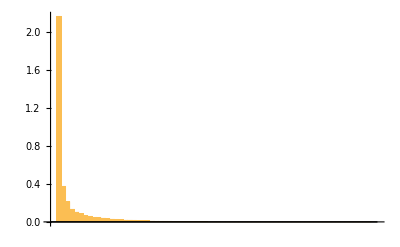

5.106

3.57329

3.57329

```mathematica
λ=Eigenvalues[X]/(Length[data]- 1);
BarChart[λ]
Variance[data]//Total
Variance[projectedData]//Total
λ//Total
```

```mathematica
P={x,y};
checkOrthonormality=P.Transpose[P]//Chop
```

{{1.,0},{0,1.}}

```mathematica
Orgn={(P.D28avg)[[1]],(P.Mean[Join[D0,Ecl]])[[2]]}
```

{0.677925,1.89433}

```mathematica
map[x_]:=P.x-Orgn
```

Plot projected data:

```mathematica
ptsD0=map/@D0;
ptsCtrl=map/@Ctrl;
ptsD28=map/@D28;
ptsEcl=map/@Ecl;
```

```mathematica
ptsAvgD0=map/@{D0avg};
ptsAvgCtrl=map/@{Ctrlavg};
ptsAvgD28=map/@{D28avg};
ptsAvgEcl=map/@{Eclavg};
```

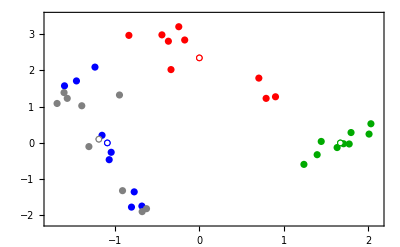

```mathematica
pl1=ListPlot[{ptsD0,ptsCtrl,ptsD28,ptsEcl},PlotStyle->{Blue,Gray,Red,Darker[Green]}];
pl2=ListPlot[{ptsAvgD0,ptsAvgCtrl,ptsAvgD28,ptsAvgEcl},PlotMarkers->{{Graphics[{EdgeForm[Blue],White,Disk[]}],0.04},{Graphics[{EdgeForm[Gray],White,Disk[]}],0.04},{Graphics[{EdgeForm[Red],White,Disk[]}],0.04},{Graphics[{EdgeForm[Darker[Green]],White,Disk[]}],0.04}}];
Show[{pl1,pl2},Frame->True]
```